```mathematica
Needs["ErrorBarPlots`"]
```

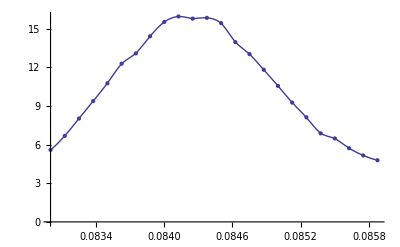

```mathematica
(*for l=30 & 40*)
v=9;
l=8;
vv=ToString[v];
ll=ToString[l];
Chi1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-1.txt",{Number,Number}];
Chit1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-1.txt",{Number,Number}];
Chi2=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-2.txt",{Number,Number}];
Chit2=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-2.txt",{Number,Number}];
Chi3=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-3.txt",{Number,Number}];
Chit3=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-3.txt",{Number,Number}];
Chi4=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-4.txt",{Number,Number}];
Chit4=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-4.txt",{Number,Number}];

Chi[v][l]=Table[{Chi1[[All,1]][[i]],(Chi1[[All,2]][[i]]+Chi2[[All,2]][[i]]+Chi3[[All,2]][[i]]+Chi4[[All,2]][[i]])/4.},{i,1,Length[Chi1]}];
Chit[v][l]=Table[{Chit1[[All,1]][[i]],(Chit1[[All,2]][[i]]+Chit2[[All,2]][[i]]+Chit3[[All,2]][[i]]+Chit4[[All,2]][[i]])/4.},{i,1,Length[Chi1]}];


(*Chi5=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-5.txt",{Number,Number}];
Chit5=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-5.txt",{Number,Number}];
Chi6=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-6.txt",{Number,Number}];
Chit6=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-6.txt",{Number,Number}];
Chi7=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-7.txt",{Number,Number}];
Chit7=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-7.txt",{Number,Number}];
Chi8=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-8.txt",{Number,Number}];
Chit8=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-8.txt",{Number,Number}];


Chi[v][l]=Table[{Chi1[[All,1]][[i]],(Chi1[[All,2]][[i]]+Chi2[[All,2]][[i]]+Chi3[[All,2]][[i]]+Chi4[[All,2]][[i]]+Chi5[[All,2]][[i]]+Chi6[[All,2]][[i]]+Chi7[[All,2]][[i]]+Chi8[[All,2]][[i]])/8.},{i,1,Length[Chi1]}];
Chit[v][l]=Table[{Chit1[[All,1]][[i]],(Chit1[[All,2]][[i]]+Chit2[[All,2]][[i]]+Chit3[[All,2]][[i]]+Chit4[[All,2]][[i]]+Chit5[[All,2]][[i]]+Chit6[[All,2]][[i]]+Chit7[[All,2]][[i]]+Chit8[[All,2]][[i]])/8.},{i,1,Length[Chi1]}];*)

(*for l=30 & 40*)
(*Chi9=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-9.txt",{Number,Number}];
Chit9=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-9.txt",{Number,Number}];
Chi10=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-10.txt",{Number,Number}];
Chit10=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-10.txt",{Number,Number}];
Chi11=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-11.txt",{Number,Number}];
Chit11=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-11.txt",{Number,Number}];
Chi12=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-12.txt",{Number,Number}];
Chit12=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-12.txt",{Number,Number}];

Chi[v][l]=Table[{Chi1[[All,1]][[i]],(Chi1[[All,2]][[i]]+Chi2[[All,2]][[i]]+Chi3[[All,2]][[i]]+Chi4[[All,2]][[i]]+Chi5[[All,2]][[i]]+Chi6[[All,2]][[i]]+Chi7[[All,2]][[i]]+Chi8[[All,2]][[i]]+Chi9[[All,2]][[i]]+Chi10[[All,2]][[i]]+Chi11[[All,2]][[i]]+Chi12[[All,2]][[i]])/12.},{i,1,Length[Chi1]}];
Chit[v][l]=Table[{Chit1[[All,1]][[i]],(Chit1[[All,2]][[i]]+Chit2[[All,2]][[i]]+Chit3[[All,2]][[i]]+Chit4[[All,2]][[i]]+Chit5[[All,2]][[i]]+Chit6[[All,2]][[i]]+Chit7[[All,2]][[i]]+Chit8[[All,2]][[i]]+Chit9[[All,2]][[i]]+Chit10[[All,2]][[i]]+Chit11[[All,2]][[i]]+Chit12[[All,2]][[i]])/12.},{i,1,Length[Chi1]}];*)




Cht4[v][l]=Chit[v][l];
Ch4[v][l]=Chi[v][l];

i4[v][l]=Interpolation[Ch4[v][l]];
it4[v][l]=Interpolation[Cht4[v][l]];

pic1=ListPlot[Chi[v][l],PlotRange->Full];
pic2=Plot[i4[v][l][x],{x,Chi[v][l][[All,1]][[1]],Chi[v][l][[All,1]][[Length[Chi[v][l]]]]},PlotRange->Full];
Show[{pic1,pic2}]
```

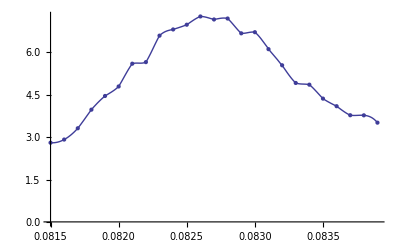

```mathematica
150, 200,4, 8:4
30, 40 :12
16,100:8
50,20,10:10
5: 2*5
```

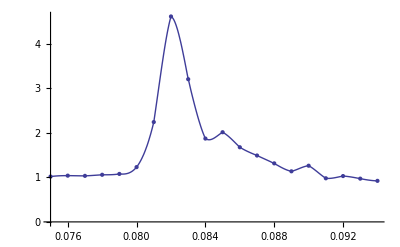

```mathematica
v=9;
l=100;
Cht4[v][l]=Chit[v][l];
Ch4[v][l]=Chi[v][l];

i4[v][l]=Interpolation[Ch4[v][l]];
it4[v][l]=Interpolation[Cht4[v][l]];

pic1=ListPlot[Chi[v][l],PlotRange->Full];
pic2=Plot[i4[v][l][x],{x,Chi[v][l][[All,1]][[1]],Chi[v][l][[All,1]][[Length[Chi[v][l]]]]},PlotRange->Full];
Show[{pic1,pic2}]
```

```mathematica
Maxx={};
Maxy={};
Do[
Do[
Maxd[v][l]=Sort[Ch4[v][l],#1[[2]]>#2[[2]]&];
Maxx=Append[Maxx,{l*1000,Maxd[v][l][[All,1]][[1]]}];
Maxy=Append[Maxy,{l*1000,Maxd[v][l][[All,2]][[1]]}];
,{v,{9}}]
,{l,{4,5,8,10,16,20,30,40,50,100,150,200}}]
```

```mathematica
Maxx={{4000,0.0855},{5000,0.085},{8000,0.084125},{10000,0.0838},{16000,0.08325},{20000,0.083},{30000,0.0827},{40000,0.0826},{50000,0.0821},{100000,0.082},{150000,0.0817},{200000,0.0817}}
Maxy={{4000,21.65885},{5000,19.60315},{8000,15.959175},{10000,14.64014},{16000,11.476725},{20000,9.729393000000002},{30000,7.3744375},{40000,6.557308333333333},{50000,6.02102},{100000,4.6185275},{150000,2.5028900000000003},{200000,2.4837325}}
```

{{4000,0.0855},{5000,0.085},{8000,0.084125},{10000,0.0838},{16000,0.08325},{20000,0.083},{30000,0.0827},{40000,0.0826},{50000,0.0821},{100000,0.082},{150000,0.0817},{200000,0.0817}}

{{4000,21.6589},{5000,19.6032},{8000,15.9592},{10000,14.6401},{16000,11.4767},{20000,9.72939},{30000,7.37444},{40000,6.55731},{50000,6.02102},{100000,4.61853},{150000,2.50289},{200000,2.48373}}

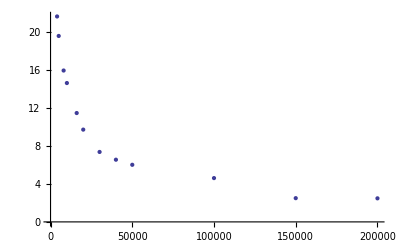

-Graphics-

```mathematica
ListPlot[Maxy]
ListPlot[Maxy]
```

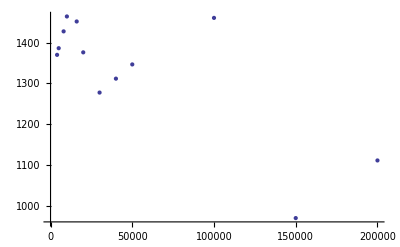

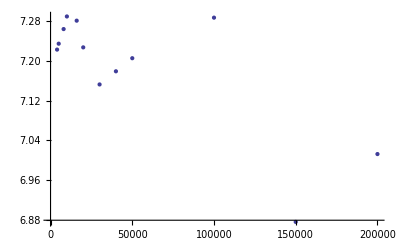

```mathematica
α=0.5;
Maxys=Table[{Maxy[[All,1]][[i]],Maxy[[All,2]][[i]]*Maxy[[All,1]][[i]]^α},{i,1,Length[Maxy]}];
Maxysl=Table[{Maxy[[All,1]][[i]],Log[Maxy[[All,2]][[i]]]+Log[Maxy[[All,1]][[i]]]*α},{i,1,Length[Maxy]}];
ListPlot[Maxys]
ListPlot[Maxysl]
```

fit :  (0.0812201+0.374587/x^0.54)

0.997587 = r0

0.54 = z0

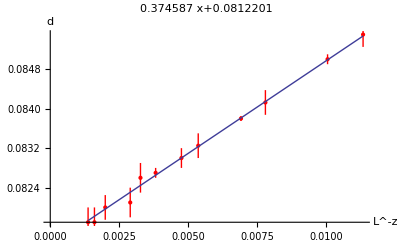

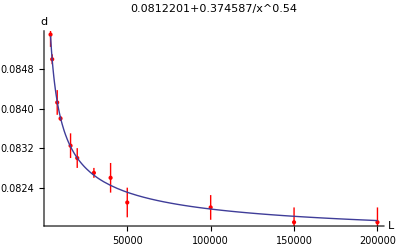

{0.0812201+0.374587/x^0.54, | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.0812201 | 0.000040313 | 2014.74 | 2.23312×10^-29
1/x^0.54 | 0.374587 | 0.0058264 | 64.2914 | 2.01725×10^-14}

FittedModel[-0.871009-0.551967 x]

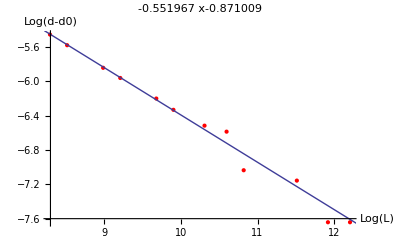

{-0.871009-0.551967 x, | Estimate | Standard Error | t-Statistic | P-Value
1 | -0.871009 | 0.160193 | -5.43723 | 0.00028596
x | -0.551967 | 0.0168793 | -32.7008 | 1.68652×10^-11}

```mathematica
ClearAll[z,r,x,k]
r0=0;
For[z=0.0,z<1.5,z+=0.01;
Maxxs=Table[{Maxx[[All,1]][[i]],Maxx[[All,2]][[i]]},{i,1,Length[Maxx]}];
model=k*x^-z+d;
fit=LinearModelFit[Maxxs,{1,x^-z},x,Weights->1/Errorx^2];
(*fit=NonlinearModelFit[Maxxs,model,{k,d},x,Weights->1/Errorx^2];*)

r=fit["RSquared"];
r
If[r>r0,
ffit=fit["BestFit"];
fitf=fit;
val=fit["ParameterTableEntries"];
r0=r;
z0=z;
]


]
ffit "fit : "
r0 "= r0"
z0 "= z0"
Maxxs=Table[{Maxx[[All,1]][[i]]^-z0,Maxx[[All,2]][[i]]},{i,1,Length[Maxx]}];
errx=Table[Errorx[[i]]*(z0)*Maxx[[All,1]][[i]]^(-z0-1),{i,1,Length[Errorx]}];
maxxerrs=Table[{Maxxs[[i]],ErrorBar[Errorx[[i]]]},{i,0,Length[Errorx]}];

(*pic1=ListPlot[Maxxs,PlotStyle->Red,AxesLabel->{"L^-z","d"},PlotLabel->ffit];*)
pic1=ErrorListPlot[maxxerrs,PlotStyle->Red,AxesLabel->{"L^-z","d"},PlotLabel->val[[1]][[1]]+val[[2]][[1]]*"x"];
pic2=Plot[val[[1]][[1]]+val[[2]][[1]]*x,{x,Maxx[[All,1]][[1]]^-z0,Maxx[[All,1]][[Length[Maxx]]]^-z0}];
Show[{pic1,pic2}]
maxyerr=Table[{Maxy[[i]],ErrorBar[Errory[[i]]]},{i,0,Length[Errory]}];
maxxerr=Table[{Maxx[[i]],ErrorBar[Errorx[[i]]]},{i,0,Length[Errorx]}];
pic1=ErrorListPlot[maxxerr,PlotRange->Full,PlotStyle->Red,AxesLabel->{"L","d"},PlotLabel->ffit];
pic3=Plot[val[[1]][[1]]+val[[2]][[1]]*x^-z0,{x,4000,200000},PlotRange->Full];
Show[{pic1,pic3}]
fitf[{"BestFit","ParameterTable"}]

ClearAll[k,x,z]
Maxxzcheck=Table[{Log[Maxx[[All,1]][[i]]],Log[Maxx[[All,2]][[i]]-val[[1]][[1]]]},{i,1,Length[Maxx]}];
Errorxzcheck=Table[Errorx[[i]]/Maxxzcheck[[All,2]][[i]],{i,1,Length[Maxx]}];
model=k-z*x;
fit=LinearModelFit[Maxxzcheck,{1,x},x,Weights->1/Errorx^2]
maxxzcheckerr=Table[{Maxxzcheck[[i]],ErrorBar[Errorxzcheck[[i]]]},{i,0,Length[Errorx]}];
ffit=fit["BestFit"];
fitf=fit;
val=fit["ParameterTableEntries"];
pic1=ErrorListPlot[maxxzcheckerr,PlotRange->Full,PlotStyle->Red,AxesLabel->{"Log(L)","Log(d-d0)"},PlotLabel->ffit];
pic3=Plot[val[[1]][[1]]+val[[2]][[1]]*x,{x,7,13},PlotRange->Full];
Show[{pic1,pic3}]
fitf[{"BestFit","ParameterTable"}]
```

```mathematica
ErrorListPlot[maxxerr,PlotRange->Full,PlotStyle->Red,AxesLabel->{"L","d"},PlotLabel->ffit];
```

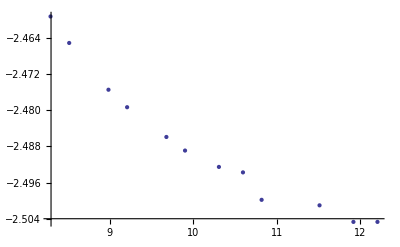

```mathematica
x=Maxx[[All,1]];
y=Maxx[[All,2]];
dat=Table[{Log[x[[i]]],Log[y[[i]]]},{i,1,Length[x]}];
pic1=ListPlot[dat]
```

```mathematica
dat
```

{{Log[4000],-2.45924},{Log[5000],-2.4651},{Log[8000],-2.47545},{Log[10000],-2.47932},{Log[16000],-2.48591},{Log[20000],-2.48891},{Log[30000],-2.49254},{Log[40000],-2.49375},{Log[50000],-2.49982},{Log[100000],-2.50104},{Log[150000],-2.5047},{Log[200000],-2.5047}}

```mathematica
ClearAll[x]
```

(1424.26 fit :)/x^0.5

0.998601 = r0

0.5 = α0

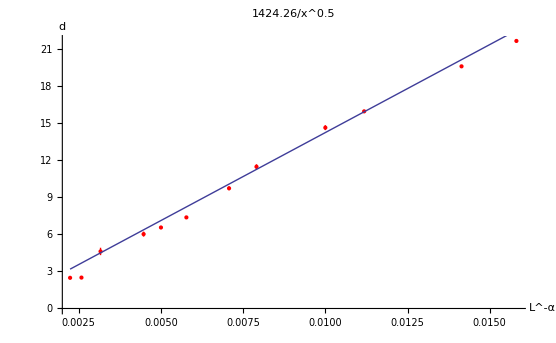

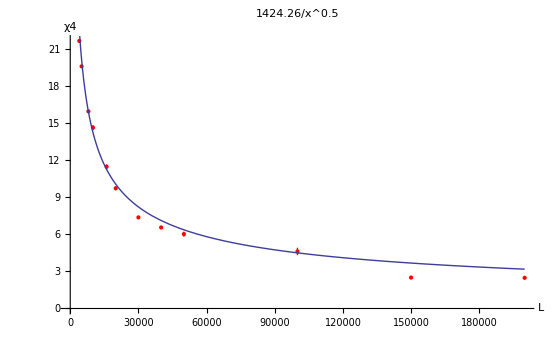

{1424.26/x^0.5, | Estimate | Standard Error | t-Statistic | P-Value
k | 1424.26 | 16.0738 | 88.6076 | 4.71824×10^-17}

```mathematica
r0=0;
For[α=0.0,α<1,α+=0.01;
Maxys=Table[{Maxy[[All,1]][[i]],Maxy[[All,2]][[i]]},{i,1,Length[Maxy]}];
model=k*x^-α;
fit=NonlinearModelFit[Maxys,model,{k},x,Weights->1/Errorx^2];

r=fit["RSquared"];
If[r>r0,
ffit=fit["BestFit"];
val=fit["ParameterTableEntries"];
r0=r;
α0=α;
fitf=fit;
]


]
ffit "fit : "
r0 "= r0"
α0 "= α0"
Maxys=Table[{Maxy[[All,1]][[i]]^-α0,Maxy[[All,2]][[i]]},{i,1,Length[Maxy]}];
erry=Table[Errory[[i]]*(α0)*Maxy[[All,1]][[i]]^(-α0-1),{i,1,Length[Errory]}];
maxyerrs=Table[{Maxys[[i]],ErrorBar[Errory[[i]]]},{i,0,Length[Errory]}];

(*pic1=ListPlot[Maxxs,PlotStyle->Red,AxesLabel->{"L^-z","d"},PlotLabel->ffit];*)
pic1=ErrorListPlot[maxyerrs,PlotStyle->Red,AxesLabel->{"L^-α","d"},PlotLabel->ffit];

(*pic1=ListPlot[Maxys,PlotStyle->Red,AxesLabel->{"L^-α","χ4"},PlotLabel->ffit];*)
pic2=Plot[val[[1]][[1]]*x,{x,Maxy[[All,1]][[1]]^-α0,Maxy[[All,1]][[Length[Maxx]]]^-α0}];
Show[{pic1,pic2}]
maxyerr=Table[{Maxy[[i]],ErrorBar[Errory[[i]]]},{i,0,Length[Errory]}];
pic1=ErrorListPlot[maxyerr,PlotStyle->Red,AxesLabel->{"L","χ4"},PlotLabel->ffit];
pic3=Plot[val[[1]][[1]]*x^-α0,{x,4000,200000},PlotRange->Full];
Show[{pic1,pic3}]
fitf[{"BestFit","ParameterTable"}]
```

fit :  (-4.90087+531.955/x^0.36)

0.992148 = r0

0.36 = α0

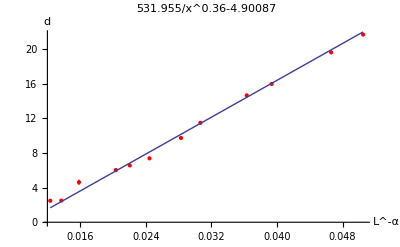

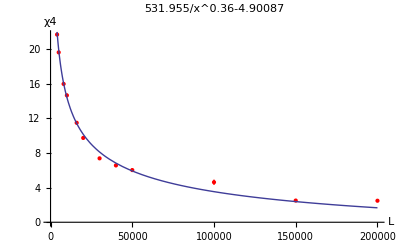

{-4.90087+531.955/x^0.36, | Estimate | Standard Error | t-Statistic | P-Value
1 | -4.90087 | 0.530758 | -9.23372 | 3.28423×10^-6
1/x^0.36 | 531.955 | 14.9647 | 35.5472 | 7.36802×10^-12}

```mathematica
ClearAll[z,r,x]
r0=0;
For[α=0.0,α<1,α+=0.01;
Maxys=Table[{Maxy[[All,1]][[i]],Maxy[[All,2]][[i]]},{i,1,Length[Maxy]}];
model=k*x^-α;
fit=LinearModelFit[Maxys,{1,x^-α},x,Weights->1/Errorx^2];

r=fit["RSquared"];
If[r>r0,
ffit=fit["BestFit"];
val=fit["ParameterTableEntries"];
r0=r;
α0=α;
fitf=fit;
]


]
ffit "fit : "
r0 "= r0"
α0 "= α0"
Maxys=Table[{Maxy[[All,1]][[i]]^-α0,Maxy[[All,2]][[i]]},{i,1,Length[Maxy]}];
erry=Table[Errory[[i]]*(α0)*Maxy[[All,1]][[i]]^(-α0-1),{i,1,Length[Errory]}];
maxyerrs=Table[{Maxys[[i]],ErrorBar[Errory[[i]]]},{i,0,Length[Errory]}];

(*pic1=ListPlot[Maxxs,PlotStyle->Red,AxesLabel->{"L^-z","d"},PlotLabel->ffit];*)
pic1=ErrorListPlot[maxyerrs,PlotStyle->Red,AxesLabel->{"L^-α","d"},PlotLabel->ffit];

(*pic1=ListPlot[Maxys,PlotStyle->Red,AxesLabel->{"L^-α","χ4"},PlotLabel->ffit];*)
pic2=Plot[val[[1]][[1]]+val[[2]][[1]]*x,{x,Maxy[[All,1]][[1]]^-α0,Maxy[[All,1]][[Length[Maxx]]]^-α0}];
Show[{pic1,pic2}]
maxyerr=Table[{Maxy[[i]],ErrorBar[Errory[[i]]]},{i,0,Length[Errory]}];
pic1=ErrorListPlot[maxyerr,PlotStyle->Red,AxesLabel->{"L","χ4"},PlotLabel->ffit];
pic3=Plot[val[[1]][[1]]+val[[2]][[1]]*x^-α0,{x,4000,200000},PlotRange->Full];
Show[{pic1,pic3}]
fitf[{"BestFit","ParameterTable"}]
```

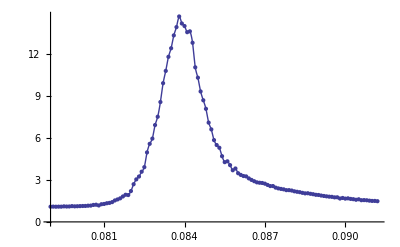

```mathematica
v=9;
l=10;
pic1=ListPlot[Chi[v][l],PlotRange->Full];
pic2=Plot[i4[v][l][x],{x,Chi[v][l][[All,1]][[1]],Chi[v][l][[All,1]][[Length[Chi[v][l]]]]},PlotRange->Full];
Show[{pic1,pic2}]
```

```mathematica
l=10;
Do[
z=0.51;
d0=0.081;
α=0.52;
scale[l]=Table[{(Chi[v][l][[All,1]][[i]]-d0)*((l*1000.)^z),Log[Chi[v][l][[All,2]][[i]]]+α*Log[l*1000.]},{i,1,Length[Chi[v][l]]}];
,{l,{4,5,8,10,16,20,30,40,50,100,150,200}}]
```

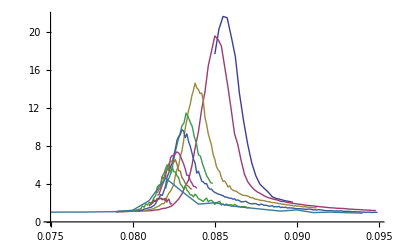

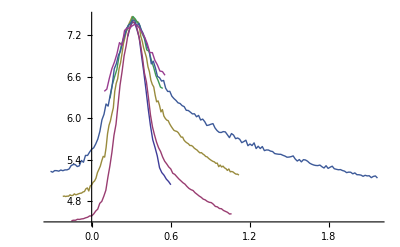

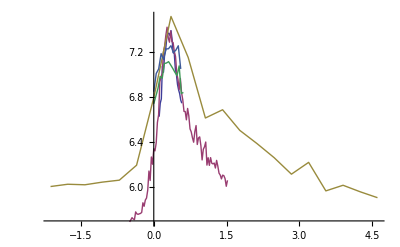

```mathematica
ListLinePlot[{Chi[v][4],Chi[v][5],Chi[v][10],Chi[v][16],Chi[v][20],Chi[v][30],Chi[v][40],Chi[v][50],Chi[v][100],Chi[v][150],Chi[v][200]},PlotRange->Full]
ListLinePlot[{scale[4],scale[5],scale[10],scale[16],scale[20],scale[30]},PlotRange->Full]
ListLinePlot[{scale[40],scale[50],scale[100],scale[150],scale[200]},PlotRange->Full]
```

```mathematica
Maxd[9][100]
```

{{0.082,4.61853},{0.0825,4.04458},{0.0815,3.97664},{0.083,3.20819},{0.0835,2.24727},{0.081,2.24466},{0.085,2.01591},{0.0845,1.92668},{0.084,1.87353},{0.0855,1.83983},{0.086,1.67808},{0.0875,1.63449},{0.0805,1.58105},{0.0865,1.5473},{0.087,1.4924},{0.088,1.31607},{0.0885,1.29558},{0.09,1.26303},{0.0895,1.25915},{0.08,1.2314},{0.0795,1.18312},{0.089,1.1372},{0.0785,1.08325},{0.079,1.07834},{0.078,1.05944},{0.0905,1.05777},{0.0775,1.04803},{0.0765,1.04045},{0.076,1.03987},{0.077,1.03502},{0.092,1.03051},{0.0755,1.02597},{0.075,1.01905},{0.0925,1.00903},{0.091,0.980276},{0.093,0.972311},{0.0935,0.946607},{0.0915,0.930128},{0.094,0.922815},{0.0945,0.870434}}

```mathematica
errorx[150]=0.0003
errory[150]=0.02
```

0.0003

0.02

```mathematica
errorx[100]
```

0.00025

```mathematica
Errorx={errorx[4],errorx[5],errorx[8],errorx[10],errorx[16],errorx[20],errorx[30],errorx[40],errorx[50],errorx[100],errorx[150],errorx[200]}
Errory={errory[4],errory[5],errory[8],errory[10],errory[16],errory[20],errory[30],errory[40],errory[50],errory[100],errory[150],errory[200]}
```

{0.00025,0.0001,0.00025,0.00005,0.00025,0.0002,0.0001,0.0003,0.0003,0.00025,0.0003,0.0003}

{0.1,0.1,0.05,0.2,0.2,0.15,0.1,0.1,0.2,0.3,0.02,0.02}

```mathematica
maxx=Table[{dataoptb01[[i]],ErrorBar[errors1[[i]]]},{i,0,Length[dataoptb01]}];
```

```mathematica
Maxys=Table[{Maxy[[All,1]][[i]]^-α0,Maxy[[All,2]][[i]]},{i,1,Length[Maxy]}];
errx=Table[Errory[[i]]*(-α0)*Maxy[[All,1]][[i]]^(-α0-1),{i,1,Length[Errory]}];
pic1=ListPlot[Maxys,PlotStyle->Red,AxesLabel->{"L^-α","χ4"},PlotLabel->ffit];
pic2=Plot[val[[1]][[1]]*x,{x,Maxy[[All,1]][[1]]^-α0,Maxy[[All,1]][[Length[Maxx]]]^-α0}];
```

```mathematica
Maxys=Table[{Maxy[[All,1]][[i]]^-α0,Maxy[[All,2]][[i]]},{i,1,Length[Maxy]}]
errx=Table[Errory[[i]]*(α0)*Maxy[[All,1]][[i]]^(-α0-1),{i,1,Length[Errory]}]
```

{{0.0133946,21.6589},{0.0119271,19.6032},{0.009341,15.9592},{0.00831764,14.6401},{0.00651415,11.4767},{0.00580049,9.72939},{0.00469783,7.37444},{0.0040451,6.55731},{0.00360193,6.02102},{0.00251189,4.61853},{0.00203438,2.50289},{0.00175172,2.48373}}

{1.74129×10^-7,1.24042×10^-7,3.03582×10^-8,8.65034×10^-8,4.2342×10^-8,2.26219×10^-8,8.1429×10^-9,5.25862×10^-9,7.49202×10^-9,3.91854×10^-9,1.4105×10^-10,9.10894×10^-11}

```mathematica
Maxy
```

{{4000,21.6589},{5000,19.6032},{8000,15.9592},{10000,14.6401},{16000,11.4767},{20000,9.72939},{30000,7.37444},{40000,6.55731},{50000,6.02102},{100000,4.61853},{150000,2.50289},{200000,2.48373}}

```mathematica
maxyerr=Table[{Maxy[[i]],ErrorBar[Errory[[i]]]},{i,0,Length[Errory]}];
maxxerr=Table[{Maxx[[i]],ErrorBar[Errorx[[i]]]},{i,0,Length[Errorx]}];
ErrorListPlot[maxxerr,PlotRange->Full]
ErrorListPlot[maxyerr]
```

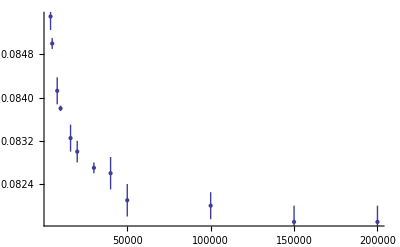

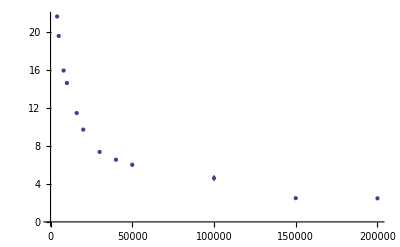

```mathematica
ErrorListPlot[maxxerr,PlotRange->Full]
ErrorListPlot[maxyerr]
```